# Department Numbers

There is a highly organized city that has decided to assign a number to each of their departments:

police department

sanitation department

fire department

The conditions are as follows

Each department can have a number between   1   and   7   (inclusive).

The three department numbers are to be unique (different from each other) and must add up to   12.

The Chief of the Police doesn’t like odd numbers and wants to have an even number for his department.

#### Task

Write a computer program which outputs all valid combinations .

```mathematica
c=Cases[Permutations[Range[7],{3}],{x_?EvenQ,y_,z_}/;x+y+z==12->{x,y,z}];
Grid[Prepend[c,{"P","S","F"}],Frame->All,FrameStyle->Red]
```

P | S | F
2 | 3 | 7
2 | 4 | 6
2 | 6 | 4
2 | 7 | 3
4 | 1 | 7
4 | 2 | 6
4 | 3 | 5
4 | 5 | 3
4 | 6 | 2
4 | 7 | 1
6 | 1 | 5
6 | 2 | 4
6 | 4 | 2
6 | 5 | 1

# Deming's Funnel

Simulate dropping a marble down a funnel at target.

First run: The target is fixed.

Second run: The target is moved in the opposite direction from where the marble fell relative to the target

Third run: The target is fixed and the funnel is moved as the marble is dropped relative to the fixed target.

Fourth run: Move the funnel over exactly where the last target dropped.

## First Run

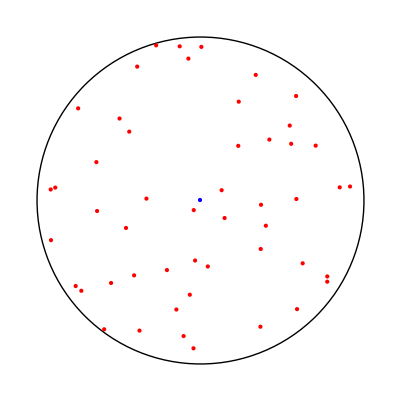

```mathematica
With[{target={0,0}},
Graphics[{Circle[target,1],{Red,Point[RandomPoint[Disk[target,1],50]]},{Blue,Point[{target}]}}]
]
```

## Second Run

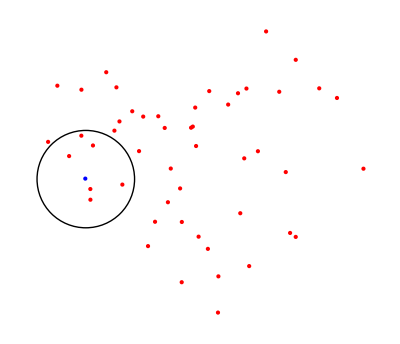

```mathematica
Module[{target={0,0},pt},
Reap[Do[
pt=Sow[RandomPoint[Disk[target,1]]];
target = -(pt-target)+target,
50]
]][[2,1]]//Graphics[{Circle[{0,0},1],{Red,Point[#]},{Blue,Point[{0,0}]}}]&
```

## Third Run

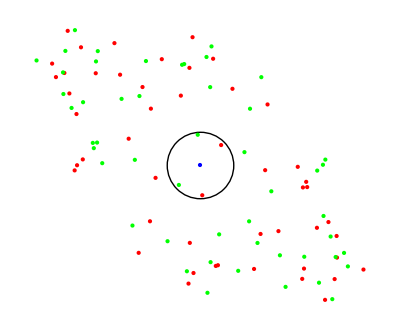

```mathematica
Graphics[{Circle[{0,0},1],{Red,Point[#[[All,1]]]},{Green,Point[#[[All,2]]]},{Blue,Point[{0,0}]}}]&@Module[{funnel={0,0},target={0,0},pt},
Reap[Do[
pt=RandomPoint[Disk[funnel,1]];
funnel = -(pt-target)+target;
Sow[{pt,funnel}];
,
50]
]][[2,1]]
```

```mathematica
Graphics[{Circle[{0,0},1],{Red,Point[#1]},{Green,Point[#2]},{Blue,Point[{0,0}]}}]&
```

## Fourth Run

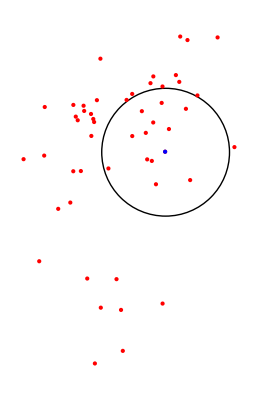

```mathematica
NestList[
RandomPoint[Disk[#,1]]&,{0,0},50]//Graphics[{Circle[{0,0},1],{Red,Point[#]},{Blue,Point[{0,0}]}}]&
```